```mathematica
CloudDeploy[ExportForm["<h1>hi</h1>","HTML"],"junk/thing",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/mukilankarthikeyan357/junk/thing]

```mathematica
CloudDeploy[Delayed[Now],"junk/thing",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/mukilankarthikeyan357/junk/thing]

```mathematica
CloudDeploy[Delayed[data=HTTPRequestData[];data["Parameters"]],"junk/thing",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/mukilankarthikeyan357/junk/thing]

```mathematica
CloudDeploy[FormPage[{"x"->"Integer"},Function[{formValues},formValues]],"junk/thing",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/mukilankarthikeyan357/junk/thing]

```mathematica
CloudDeploy[FormPage[{"x"->"Integer"},Function[{formValues},formValues]],"junk/thing",Permissions->"Public"]
```

```mathematica
?CloudDeploy
```

```mathematica
?liveAnimation
```

```mathematica
?Animate
```

#### Creating the Graphics of the Circles

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

```mathematica
Animate[Graphics[{Line[{{0,0},{5*Cos[time],5*Sin[time]}}],Circle[{0,0},5]}],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[Graphics[{Line[{{0,0},{5*Cos[-time],5*Sin[-time]}}],Circle[{0,0},5]}],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
?Circle
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[-time],5*Sin[-time]}}],
Circle[{0,0},5],
Circle[{5*Cos[-time],5*Sin[-time]},2]
}
],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],
Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[time]+5*Cos[time],2*Sin[time]+5*Sin[time]}}]
}
],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],
Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]}}]
}
],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]}}],

Circle[{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]},1],


}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]}}],

Circle[{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]},1],
Line[{{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]},{5*Cos[time]+2*Cos[2time]+Cos[3time],5*Sin[time]+2*Sin[2time]+Sin[3time]}}]

}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},3],
Line[{{5*Cos[time],5*Sin[time]},{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]}}],

Circle[{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},2],
Line[{{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]}}],

Circle[{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},1],
Line[{{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time]+Cos[4time],5*Sin[time]+3*Sin[2time]+2Sin[3time]+Sin[4time]}}]

}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]}}],

Circle[{2*Cos[2time]+5*Cos[time],2*Sin[2time]+5*Sin[time]},1],
Line[{{3*Cos[2time]+5*Cos[time],3*Sin[2time]+5*Sin[time]},{5*Cos[time]+3*Cos[2time]+2Cos[3time],5*Sin[time]+3*Sin[2time]+2Sin[3time]}}]

}
],
{time,0,2*Pi},AnimationRunning->False]
```

### Creating the the extended infinite line

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],
Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[3time]+5*Cos[time],2*Sin[3time]+5*Sin[time]}}],
Line[{{2*Cos[3time]+5*Cos[time],2*Sin[3time]+5*Sin[time]},{15,2*Sin[3time]+5*Sin[time]}}]
}
],{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
?Trace
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],
Line[{{5*Cos[time],5*Sin[time]},{10,5*Sin[time]}}]
}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],

Circle[{5*Cos[time],5*Sin[time]},2],
Line[{{5*Cos[time],5*Sin[time]},{2*Cos[3time]+5*Cos[time],2*Sin[3time]+5*Sin[time]}}],

Circle[{2*Cos[3time]+5*Cos[time],2*Sin[3time]+5*Sin[time]},1],
Line[{{2*Cos[3time]+5*Cos[time],2*Sin[3time]+5*Sin[time]},{5*Cos[time]+2*Cos[3time]+Cos[5time],5*Sin[time]+2*Sin[3time]+Sin[5time]}}],

Line[{{5*Cos[time]+2*Cos[3time]+Cos[5time],5*Sin[time]+2*Sin[3time]+Sin[5time]},{15,5*Sin[time]+2*Sin[3time]+Sin[5time]}}]
}
],
{time,0,2*Pi},AnimationRunning->False]
```

```mathematica
pointValues={}
Table[AppendTo[pointValues,{xValue,5*Sin[xValue]}],{xValue,0,2Pi}]
Animate[
Graphics[
{
Line[{{0,0},{5*Cos[time],5*Sin[time]}}],
Circle[{0,0},5],
Line[{{5*Cos[time],5*Sin[time]},{10,5*Sin[time]}}]
}
],
{time,0,2*Pi},AnimationRunning->False]
```

{}

{{{0,0}},{{0,0},{1,5 Sin[1]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]},{5,5 Sin[5]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]},{5,5 Sin[5]},{6,5 Sin[6]}}}

```mathematica
pointValues={}
Table[AppendTo[pointValues,{xValue,5*Sin[xValue]}],{xValue,0,2Pi}]
```

{}

{{{0,0}},{{0,0},{1,5 Sin[1]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]},{5,5 Sin[5]}},{{0,0},{1,5 Sin[1]},{2,5 Sin[2]},{3,5 Sin[3]},{4,5 Sin[4]},{5,5 Sin[5]},{6,5 Sin[6]}}}

```mathematica
ListPlot[]
```

-Graphics-

```mathematica
pointXValues={}
```

{}

```mathematica
pointGenerateXvalue[]:=Last[Table[AppendTo[pointXValues,xValue],{xValue,0,2Pi,Pi/50}]]
```

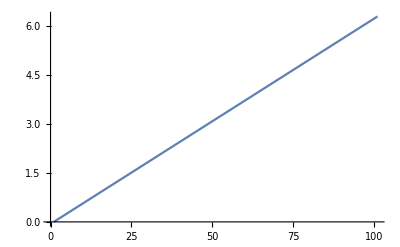

```mathematica
pointGenerateXvalue[]//ListLinePlot
```

```mathematica
ListLinePlot[5*Sin[#]]&/@pointGenerateXvalue[]
```

ListLinePlot::lpn: 0. is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: 0.313953 is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: 0.626666 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

{ListLinePlot[0],ListLinePlot[5 Sin[π/50]],ListLinePlot[5 Sin[π/25]],ListLinePlot[5 Sin[(3 π)/50]],ListLinePlot[5 Sin[(2 π)/25]],ListLinePlot[5/4 (-1+√5)],ListLinePlot[5 Sin[(3 π)/25]],ListLinePlot[5 Sin[(7 π)/50]],ListLinePlot[5 Sin[(4 π)/25]],ListLinePlot[5 Sin[(9 π)/50]],ListLinePlot[5 √(5/8-(√5)/8)],ListLinePlot[5 Sin[(11 π)/50]],ListLinePlot[5 Sin[(6 π)/25]],ListLinePlot[5 Cos[(6 π)/25]],ListLinePlot[5 Cos[(11 π)/50]],ListLinePlot[5/4 (1+√5)],ListLinePlot[5 Cos[(9 π)/50]],ListLinePlot[5 Cos[(4 π)/25]],ListLinePlot[5 Cos[(7 π)/50]],ListLinePlot[5 Cos[(3 π)/25]],ListLinePlot[5 √(5/8+(√5)/8)],ListLinePlot[5 Cos[(2 π)/25]],ListLinePlot[5 Cos[(3 π)/50]],ListLinePlot[5 Cos[π/25]],ListLinePlot[5 Cos[π/50]],ListLinePlot[5],ListLinePlot[5 Cos[π/50]],ListLinePlot[5 Cos[π/25]],ListLinePlot[5 Cos[(3 π)/50]],ListLinePlot[5 Cos[(2 π)/25]],ListLinePlot[5 √(5/8+(√5)/8)],ListLinePlot[5 Cos[(3 π)/25]],ListLinePlot[5 Cos[(7 π)/50]],ListLinePlot[5 Cos[(4 π)/25]],ListLinePlot[5 Cos[(9 π)/50]],ListLinePlot[5/4 (1+√5)],ListLinePlot[5 Cos[(11 π)/50]],ListLinePlot[5 Cos[(6 π)/25]],ListLinePlot[5 Sin[(6 π)/25]],ListLinePlot[5 Sin[(11 π)/50]],ListLinePlot[5 √(5/8-(√5)/8)],ListLinePlot[5 Sin[(9 π)/50]],ListLinePlot[5 Sin[(4 π)/25]],ListLinePlot[5 Sin[(7 π)/50]],ListLinePlot[5 Sin[(3 π)/25]],ListLinePlot[5/4 (-1+√5)],ListLinePlot[5 Sin[(2 π)/25]],ListLinePlot[5 Sin[(3 π)/50]],ListLinePlot[5 Sin[π/25]],ListLinePlot[5 Sin[π/50]],ListLinePlot[0],ListLinePlot[-5 Sin[π/50]],ListLinePlot[-5 Sin[π/25]],ListLinePlot[-5 Sin[(3 π)/50]],ListLinePlot[-5 Sin[(2 π)/25]],ListLinePlot[5/4 (1-√5)],ListLinePlot[-5 Sin[(3 π)/25]],ListLinePlot[-5 Sin[(7 π)/50]],ListLinePlot[-5 Sin[(4 π)/25]],ListLinePlot[-5 Sin[(9 π)/50]],ListLinePlot[-5 √(5/8-(√5)/8)],ListLinePlot[-5 Sin[(11 π)/50]],ListLinePlot[-5 Sin[(6 π)/25]],ListLinePlot[-5 Cos[(6 π)/25]],ListLinePlot[-5 Cos[(11 π)/50]],ListLinePlot[5/4 (-1-√5)],ListLinePlot[-5 Cos[(9 π)/50]],ListLinePlot[-5 Cos[(4 π)/25]],ListLinePlot[-5 Cos[(7 π)/50]],ListLinePlot[-5 Cos[(3 π)/25]],ListLinePlot[-5 √(5/8+(√5)/8)],ListLinePlot[-5 Cos[(2 π)/25]],ListLinePlot[-5 Cos[(3 π)/50]],ListLinePlot[-5 Cos[π/25]],ListLinePlot[-5 Cos[π/50]],ListLinePlot[-5],ListLinePlot[-5 Cos[π/50]],ListLinePlot[-5 Cos[π/25]],ListLinePlot[-5 Cos[(3 π)/50]],ListLinePlot[-5 Cos[(2 π)/25]],ListLinePlot[-5 √(5/8+(√5)/8)],ListLinePlot[-5 Cos[(3 π)/25]],ListLinePlot[-5 Cos[(7 π)/50]],ListLinePlot[-5 Cos[(4 π)/25]],ListLinePlot[-5 Cos[(9 π)/50]],ListLinePlot[5/4 (-1-√5)],ListLinePlot[-5 Cos[(11 π)/50]],ListLinePlot[-5 Cos[(6 π)/25]],ListLinePlot[-5 Sin[(6 π)/25]],ListLinePlot[-5 Sin[(11 π)/50]],ListLinePlot[-5 √(5/8-(√5)/8)],ListLinePlot[-5 Sin[(9 π)/50]],ListLinePlot[-5 Sin[(4 π)/25]],ListLinePlot[-5 Sin[(7 π)/50]],ListLinePlot[-5 Sin[(3 π)/25]],ListLinePlot[5/4 (1-√5)],ListLinePlot[-5 Sin[(2 π)/25]],ListLinePlot[-5 Sin[(3 π)/50]],ListLinePlot[-5 Sin[π/25]],ListLinePlot[-5 Sin[π/50]],ListLinePlot[0],ListLinePlot[0],ListLinePlot[5 Sin[π/50]],ListLinePlot[5 Sin[π/25]],ListLinePlot[5 Sin[(3 π)/50]],ListLinePlot[5 Sin[(2 π)/25]],ListLinePlot[5/4 (-1+√5)],ListLinePlot[5 Sin[(3 π)/25]],ListLinePlot[5 Sin[(7 π)/50]],ListLinePlot[5 Sin[(4 π)/25]],ListLinePlot[5 Sin[(9 π)/50]],ListLinePlot[5 √(5/8-(√5)/8)],ListLinePlot[5 Sin[(11 π)/50]],ListLinePlot[5 Sin[(6 π)/25]],ListLinePlot[5 Cos[(6 π)/25]],ListLinePlot[5 Cos[(11 π)/50]],ListLinePlot[5/4 (1+√5)],ListLinePlot[5 Cos[(9 π)/50]],ListLinePlot[5 Cos[(4 π)/25]],ListLinePlot[5 Cos[(7 π)/50]],ListLinePlot[5 Cos[(3 π)/25]],ListLinePlot[5 √(5/8+(√5)/8)],ListLinePlot[5 Cos[(2 π)/25]],ListLinePlot[5 Cos[(3 π)/50]],ListLinePlot[5 Cos[π/25]],ListLinePlot[5 Cos[π/50]],ListLinePlot[5],ListLinePlot[5 Cos[π/50]],ListLinePlot[5 Cos[π/25]],ListLinePlot[5 Cos[(3 π)/50]],ListLinePlot[5 Cos[(2 π)/25]],ListLinePlot[5 √(5/8+(√5)/8)],ListLinePlot[5 Cos[(3 π)/25]],ListLinePlot[5 Cos[(7 π)/50]],ListLinePlot[5 Cos[(4 π)/25]],ListLinePlot[5 Cos[(9 π)/50]],ListLinePlot[5/4 (1+√5)],ListLinePlot[5 Cos[(11 π)/50]],ListLinePlot[5 Cos[(6 π)/25]],ListLinePlot[5 Sin[(6 π)/25]],ListLinePlot[5 Sin[(11 π)/50]],ListLinePlot[5 √(5/8-(√5)/8)],ListLinePlot[5 Sin[(9 π)/50]],ListLinePlot[5 Sin[(4 π)/25]],ListLinePlot[5 Sin[(7 π)/50]],ListLinePlot[5 Sin[(3 π)/25]],ListLinePlot[5/4 (-1+√5)],ListLinePlot[5 Sin[(2 π)/25]],ListLinePlot[5 Sin[(3 π)/50]],ListLinePlot[5 Sin[π/25]],ListLinePlot[5 Sin[π/50]],ListLinePlot[0],ListLinePlot[-5 Sin[π/50]],ListLinePlot[-5 Sin[π/25]],ListLinePlot[-5 Sin[(3 π)/50]],ListLinePlot[-5 Sin[(2 π)/25]],ListLinePlot[5/4 (1-√5)],ListLinePlot[-5 Sin[(3 π)/25]],ListLinePlot[-5 Sin[(7 π)/50]],ListLinePlot[-5 Sin[(4 π)/25]],ListLinePlot[-5 Sin[(9 π)/50]],ListLinePlot[-5 √(5/8-(√5)/8)],ListLinePlot[-5 Sin[(11 π)/50]],ListLinePlot[-5 Sin[(6 π)/25]],ListLinePlot[-5 Cos[(6 π)/25]],ListLinePlot[-5 Cos[(11 π)/50]],ListLinePlot[5/4 (-1-√5)],ListLinePlot[-5 Cos[(9 π)/50]],ListLinePlot[-5 Cos[(4 π)/25]],ListLinePlot[-5 Cos[(7 π)/50]],ListLinePlot[-5 Cos[(3 π)/25]],ListLinePlot[-5 √(5/8+(√5)/8)],ListLinePlot[-5 Cos[(2 π)/25]],ListLinePlot[-5 Cos[(3 π)/50]],ListLinePlot[-5 Cos[π/25]],ListLinePlot[-5 Cos[π/50]],ListLinePlot[-5],ListLinePlot[-5 Cos[π/50]],ListLinePlot[-5 Cos[π/25]],ListLinePlot[-5 Cos[(3 π)/50]],ListLinePlot[-5 Cos[(2 π)/25]],ListLinePlot[-5 √(5/8+(√5)/8)],ListLinePlot[-5 Cos[(3 π)/25]],ListLinePlot[-5 Cos[(7 π)/50]],ListLinePlot[-5 Cos[(4 π)/25]],ListLinePlot[-5 Cos[(9 π)/50]],ListLinePlot[5/4 (-1-√5)],ListLinePlot[-5 Cos[(11 π)/50]],ListLinePlot[-5 Cos[(6 π)/25]],ListLinePlot[-5 Sin[(6 π)/25]],ListLinePlot[-5 Sin[(11 π)/50]],ListLinePlot[-5 √(5/8-(√5)/8)],ListLinePlot[-5 Sin[(9 π)/50]],ListLinePlot[-5 Sin[(4 π)/25]],ListLinePlot[-5 Sin[(7 π)/50]],ListLinePlot[-5 Sin[(3 π)/25]],ListLinePlot[5/4 (1-√5)],ListLinePlot[-5 Sin[(2 π)/25]],ListLinePlot[-5 Sin[(3 π)/50]],ListLinePlot[-5 Sin[π/25]],ListLinePlot[-5 Sin[π/50]],ListLinePlot[0]}